# Symmetry test

## Initialization and options

In order to execute this notebook and run a test of symmetry it is neccesary to first compile the TnSymmetryStatistic package.

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];
```

```mathematica
Middle[l_List]:=Part[l,Floor[Length[l]/2]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};

(* Opciones de los procedimientos *)
windowsize = 252;
skip = 20;
resolution = 40;
symmetryPoints = 50;
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Load database

```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}]];
AddToDataset[database,"TrendReturns",TrendReturns,{"Prices"}];
AddToDataset[database,"DatedTrendReturns",DatedTrendReturns,{"Dates","Prices"}];
AddToDataset[database,"VelocityTrendReturns",VelocityTrendReturns,{"Prices"}];
AddToDataset[database,"DatedVelocityTrendReturns",DatedVelocityTrendReturns,{"Dates","Prices"}];
```

## Crisis dates

```mathematica
rules = {"Japanese asset\nprice bubble"-> "(a)","Tequila effect"->"(b)","Dotcom bubble"->"(c)","Subprime crisis"->"(d)","Brexit"->"(e)"};
dateNames = {"Japanese asset\nprice bubble","Tequila effect","Dotcom bubble","Subprime crisis","Brexit"}/.rules;
dateObjects = {DateObject[{1990,1,1},"Day","Gregorian",-5.],DateObject[{1994,1,1},"Day","Gregorian",-5.],DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2016,6,23},"Day","Gregorian",-5.]};

AddKeyToMarket[database[[1]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[1]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[2]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[2]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[3]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[3]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[4]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[4]],"ImportantDates"->dateObjects];

orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Returns distribution

Figures 2-(b), 2-(c) and 2-(d).

```mathematica
MakeStatisticTable[marketnames_,dists_] := Module[{gridmm},
gridmm = {Join[{""},marketnames],
Join[{"μ"},Table[Mean[i],{i,dists}]],
Join[{"σ"}, Table[StandardDeviation[i],{i,dists}]],
Join[{"Skewness"}, Table[Skewness[i],{i,dists}]],
Join[{"Kurtosis"}, Table[Kurtosis[i],{i,dists}]]};
Grid[gridmm,
Alignment->Left,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{LightGray,None},{Gray,None}}
]
];
```

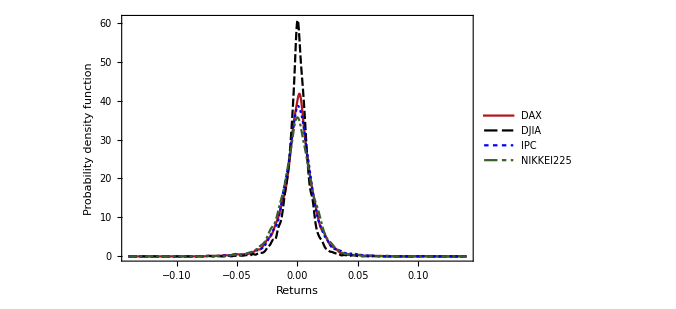

```mathematica
SmoothHistogram[database[[All,"Returns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["Returns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"Returns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000319714 | 0.000296114 | 0.000555369 | -0.0000312847
σ | 0.0142415 | 0.0107171 | 0.0148833 | 0.0151916
Skewness | -0.106661 | -0.176113 | 0.0226418 | -0.203261
Kurtosis | 7.30022 | 11.569 | 9.35525 | 8.09446

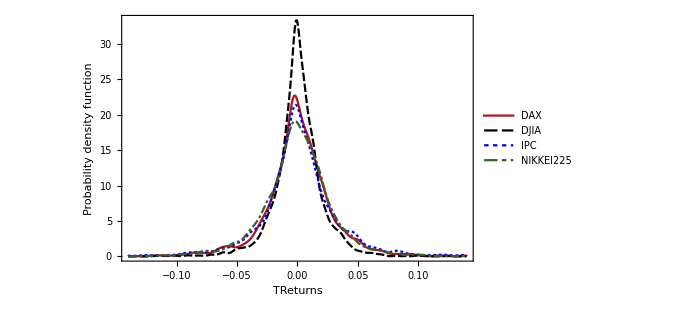

```mathematica
SmoothHistogram[database[[All,"TrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["TReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"TrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000631323 | 0.000563473 | 0.00120697 | -0.000059991
σ | 0.0295203 | 0.0208431 | 0.0342922 | 0.0300463
Skewness | -0.729049 | -0.693697 | -0.241625 | -0.569394
Kurtosis | 10.8335 | 14.9535 | 9.67833 | 11.9555

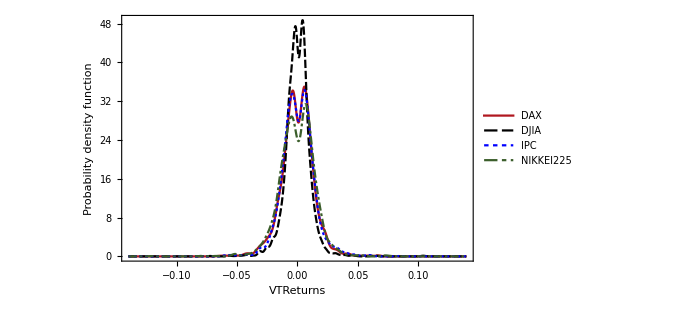

```mathematica
SmoothHistogram[database[[All,"VelocityTrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["VTReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"VelocityTrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000127415 | 0.000166781 | 0.00046062 | -0.0000621582
σ | 0.0131252 | 0.0103054 | 0.0131251 | 0.0142704
Skewness | -0.0275892 | 0.378788 | 0.152915 | -0.257632
Kurtosis | 5.43131 | 13.9691 | 5.84517 | 6.8131

```mathematica
hr = Map[{#["Name"],MeasureHeightRatio[#["VelocityTrendReturns"]]}&,database];
```

```mathematica
Grid[Prepend[hr,{"Name","Height ratio"}],Frame->All,Background->{None,{LightGray}}]
```

Name | Height ratio
DAX | 1.0235
DJIA | 1.02463
IPC | 1.02328
NIKKEI225 | 1.08783

## Symmetry plots

Figures 4, 5 and 6.

```mathematica
UpperPercentagePointLine[cmin_,cmax_,cl_]:= {{cmin, UpperPercentagePoint[cl]},{cmax,UpperPercentagePoint[cl]}};

PlotSymmetry[market_,returnType_]:= Module[{returns,standardError,tn,upperLineLimit,meanline,cMax,cMin,cFill,cline,upp,plotData,legend,p},
returns = market[returnType];
standardError = StandardDeviation[returns] / Sqrt[Length[returns]];
tn = MeasureTn[returns];
upperLineLimit = Max[tn["TnValues"][[All,2]]];

(* Plot lines *)
meanline=Line[{{Mean[returns],0},{Mean[returns],upperLineLimit/2.5}}];

cMin = Line[{{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMin"],upperLineLimit/2.5}}];
cMax = Line[{{tn["PlausibleSymmMax"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}}];
cFill = Rectangle[{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}];

cline = Line[{{MinimalBy[tn["TnValues"],Last][[1,1]],0},{MinimalBy[tn["TnValues"],Last][[1,1]],upperLineLimit/2.5}}];
upp = Map[UpperPercentagePointLine[tn["MinimumC"],tn["MaximumC"],#]&,{0.01,0.05,0.1}];
plotData = Join[{tn["TnValues"]},upp];

If[market["Name"] == "DJIA",
legend = Placed[LineLegend[{"T_n","99% CL","95% CL","90% CL"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Top}];
,
legend = None
];

p = ListLinePlot[plotData,
PlotTheme->"Monochrome",
FrameLabel->{
Style["c",bigFontSize],
Style["T_n(c)",bigFontSize]
},
Epilog->{
meanline,
cline,
cMin,
cMax,

{
Gray,
Opacity[0.4],
cFill
},

Inset[Text["μ"],{Mean[returns],upperLineLimit/2}],
Inset[Text["C_Max"],{tn["PlausibleSymmMax"],upperLineLimit/2}],
Inset[Text["C_Min"],{tn["PlausibleSymmMin"],upperLineLimit/2}],
Inset[Text["C"],{MinimalBy[tn["TnValues"],Last][[1,1]],1.7+upperLineLimit/2}]
},
PlotLegends->legend, 
PlotLabel->market["Name"],ImageSize->plotSize,Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,PlotMarkers->None, PlotStyle->colors
];
Return[p];
];
```

Returns

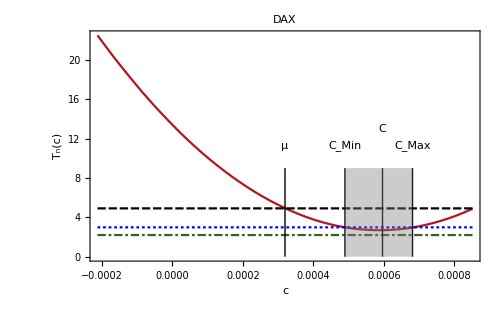
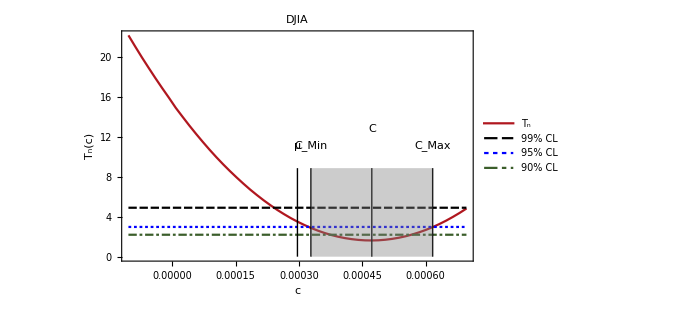
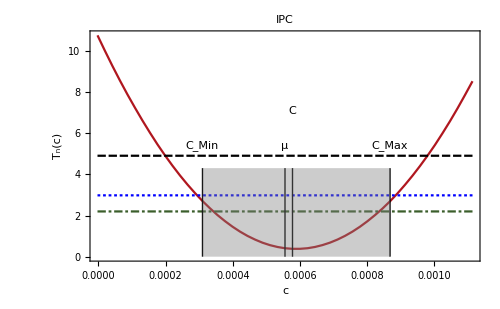
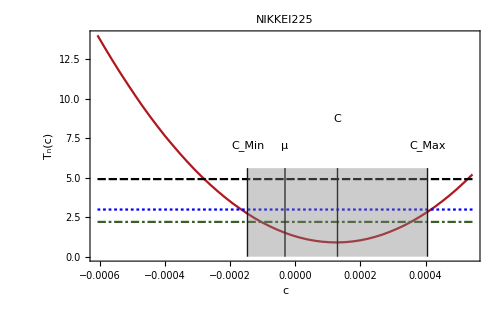

```mathematica
ProgressMap[PlotSymmetry[#,"Returns"]&,database]
```

Trend returns

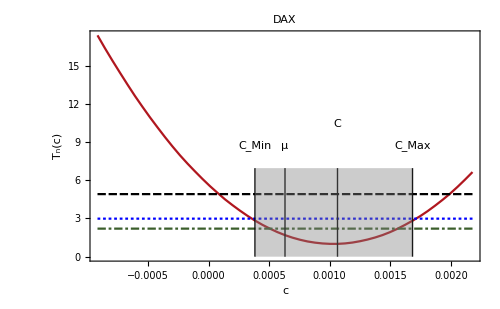
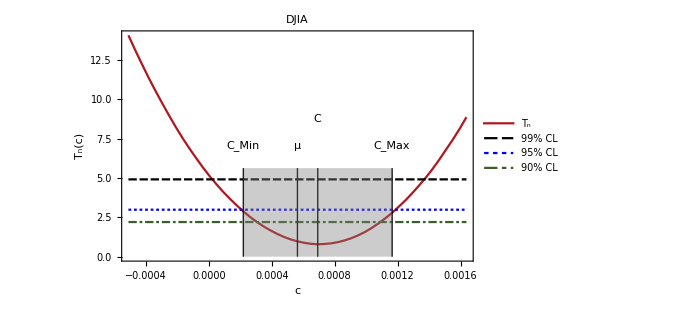
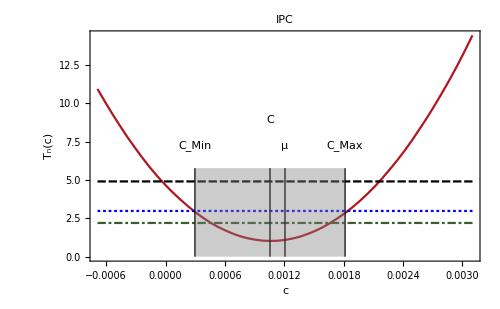
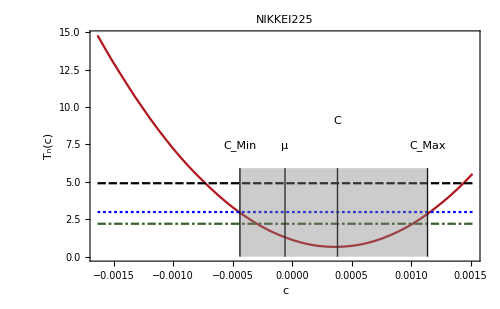

```mathematica
Map[PlotSymmetry[#,"TrendReturns"]&,database]
```

Velocity trend returns

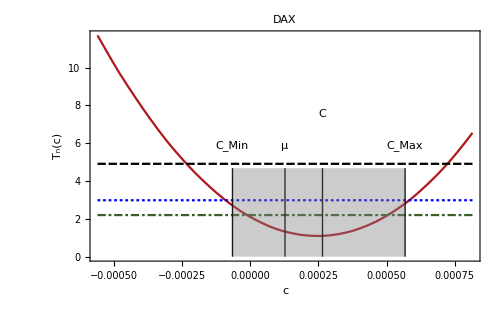
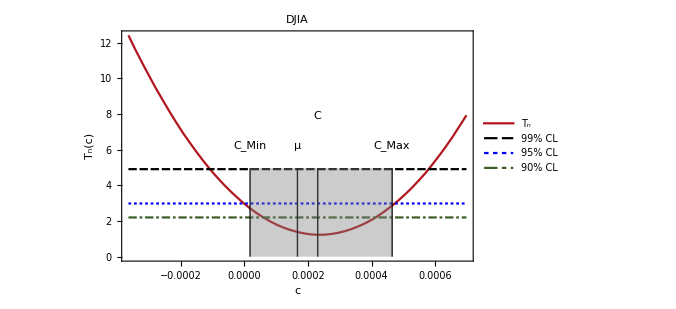
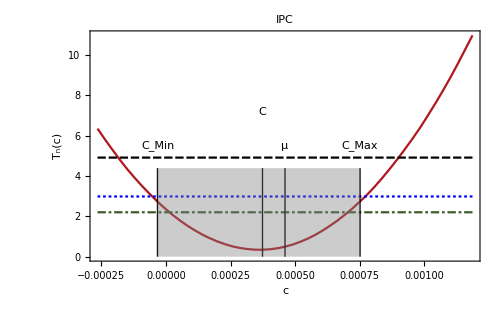
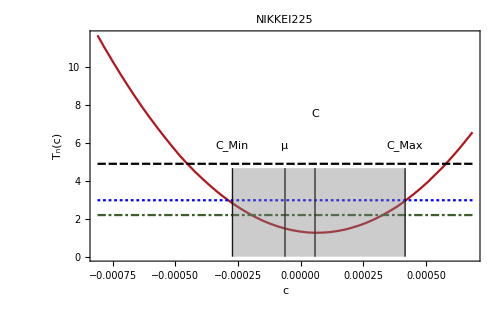

```mathematica
Map[PlotSymmetry[#,"VelocityTrendReturns"]&,database]
```

## Best symmetry point

Figure 8 and 9

```mathematica
CInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Module[{parts,partTr,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList =ProgressMap[
{Last[#[[All,1]]],MeasureTn[ #[[All,2] ]]["BestSymmetry"]}&,
parts,
"Label"->StringJoin["Calculating C in time for ",market["Name"]]
];
Return[CList];
];

μInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Module[{parts,partTr,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList =ProgressMap[{Last[#[[All,1]]],Mean[#[[All,2]]]}&,parts];
Return[CList];
];
```

```mathematica
ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];
MakeDateInverval[{first_,last_},{min_,max_}]:=Block[{cMin, cMax, cFill},
cMin = Line[{{first,min-10*Abs[min]},{first,max+10*Abs[max]}}];
cMax = Line[{{last,min-10*Abs[min]},{last,max+10*Abs[max]}}];
cFill = {Opacity[0.3],Rectangle[{first,min-10*Abs[min]},{last,max+10*Abs[max]}]};
{cMin,cMax,cFill}
];

PlotCInTime[market_,returnFunction_,windowSize_:252,skip_:40]:=Block[{plotData,p,crashLabels},
plotData = CInTime[market,returnFunction,windowSize,skip];
crashLabels = MapThread[
Callout[
ClosestDate[plotData,#1],#2,Above,
LeaderSize->35,CalloutStyle->Directive[Black,Thick],Appearance->"SlantedLabel"
]&,
{market["ImportantDates"],market["ImportantDatesNames"]}
];

p = DateListPlot[
{plotData,crashLabels},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], "C"}, 

ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotMarkers->None,
PlotRange->{{DateObject[{1989,1,1}],DateObject[{2018,9,24},"Day","Gregorian",-5.]},All},
PlotRangePadding->Automatic,
GridLines->{{},{0}},
Joined->{True,False},
PlotStyle->newColors,
PlotLabel->market["Name"]
];
Return[p];
]
```

Simple returns

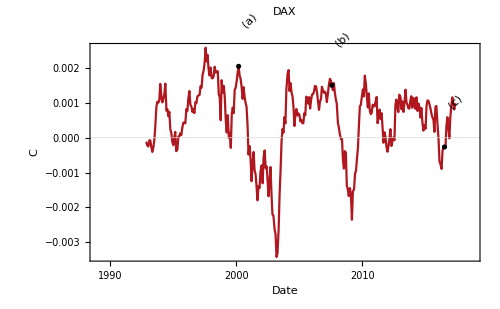
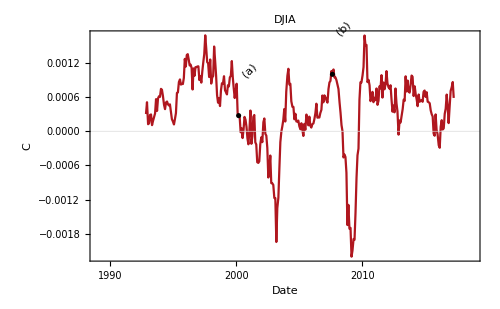
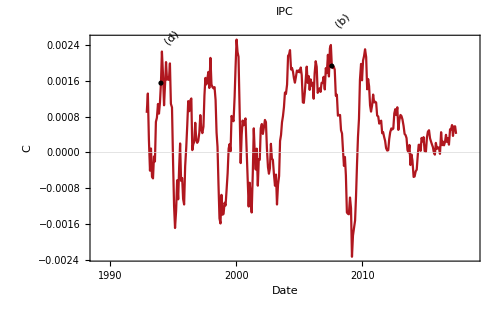
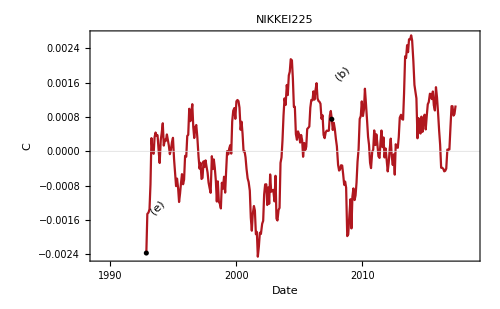

```mathematica
Map[PlotCInTime[#,"DatedReturns",windowsize,skip]&,database]
```

Trend returns

Compensa el tamaño de la ventana para que aun así represente 252 trading days.

```mathematica
TRScaleCompensate[n_,market_]:=n/Round[Mean[TrendDuration[market["Prices"]]]];
```

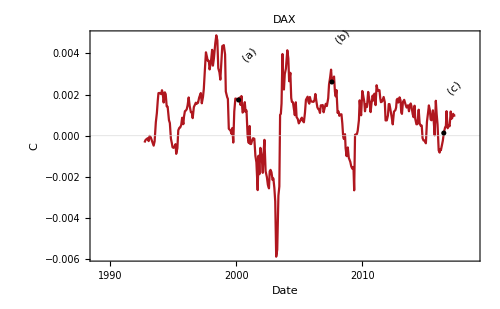
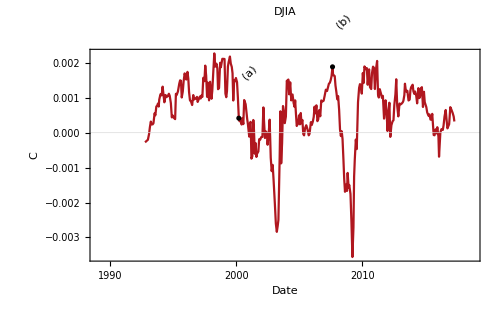
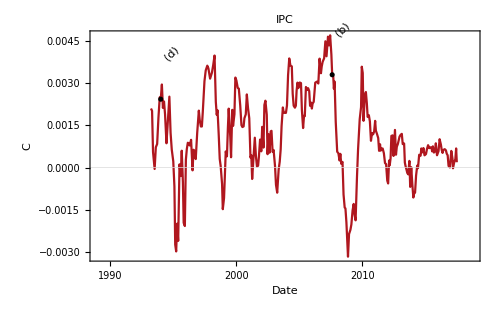
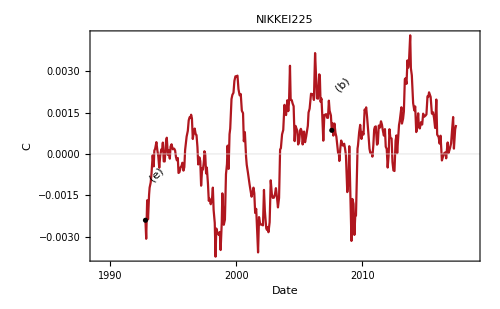

```mathematica
Map[PlotCInTime[#,"DatedTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

## Symmetry around C

```mathematica
TnCInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Block[{parts,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList = Map[{Last[#[[All,1]]],MeasureTn[#[[All,2]], 0.05]["Tn(C)"]}&,parts];
Return[CList];
];
PlotTnCInTimeInCrisis[market_,returnFunction_,windowSize_:252,skip_:40]:=Block[{plotData,uppList,actualReturnType,p,crashLabels,firstDate,lastDate,legends},
plotData =TnCInTime[market,returnFunction,windowSize,skip];
crashLabels = MapThread[
Callout[
ClosestDate[plotData,#1],#2,Above,
LeaderSize->35,CalloutStyle->Directive[Black,Thick],Appearance->"SlantedLabel"
]&,
{market["ImportantDates"],market["ImportantDatesNames"]}
];

firstDate = DateObject[{1989,1,1}];
lastDate = DateObject[{2018,9,24},"Day","Gregorian",-5.];

uppList = Map[{{firstDate, UpperPercentagePoint[#]},{lastDate,UpperPercentagePoint[#]}}&,{0.01,0.05,0.1}];
legends = {Style["T_n(c = C)",bigFontSize],Style["99% CL",bigFontSize],Style["95% CL",bigFontSize],Style["90% CL",bigFontSize]};

p = DateListPlot[
Append[Join[{plotData},uppList],crashLabels],
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["T_n-value",bigFontSize]}, 
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotLegends->If[market["Name"] == "DJIA",Placed[LineLegend[legends,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&)],{Left,Top}],None],
PlotMarkers->None,
PlotRange->{{firstDate,lastDate},All},
PlotRangePadding->Automatic,
Joined->{True,True,True,True,False},
PlotStyle->newColors,
PlotLabel->market["Name"]
];
Return[p];
]
```

Simple returns

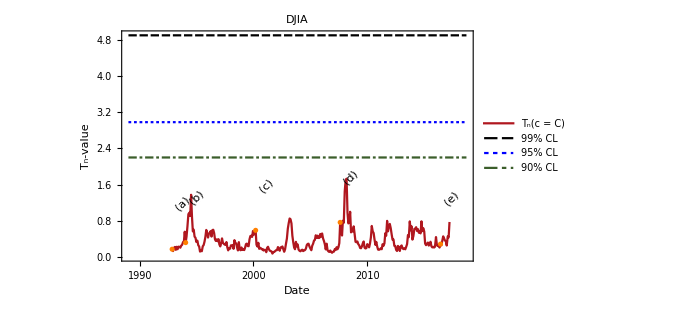
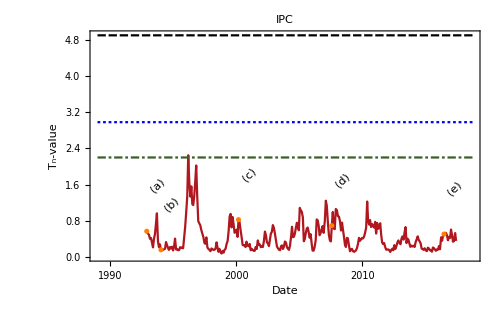
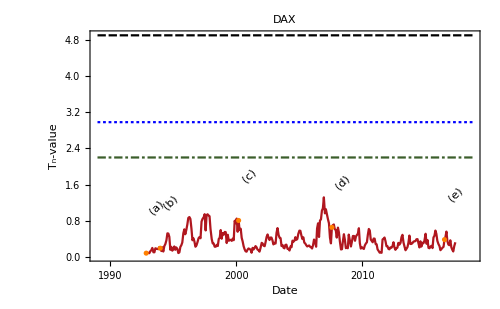
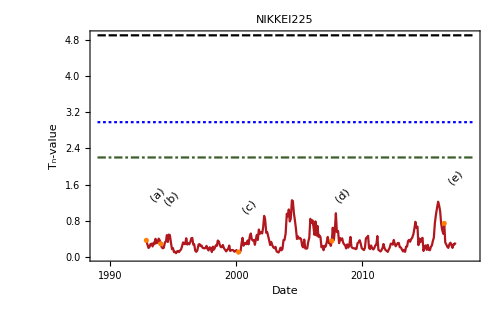

```mathematica
Map[PlotTnCInTimeInCrisis[#,"DatedReturns",windowsize,skip]&,orderedDatabase]
```

Trend returns

It is always possible to pick a plausible point of symmetry, this is not always the case for simple returns.

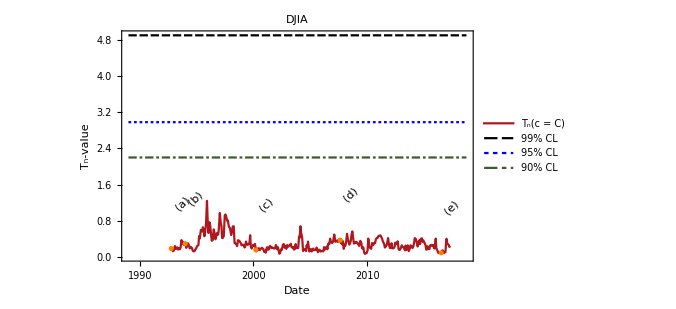
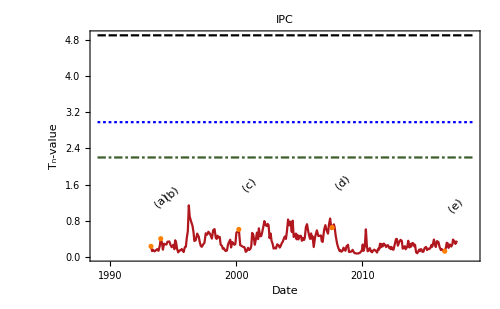
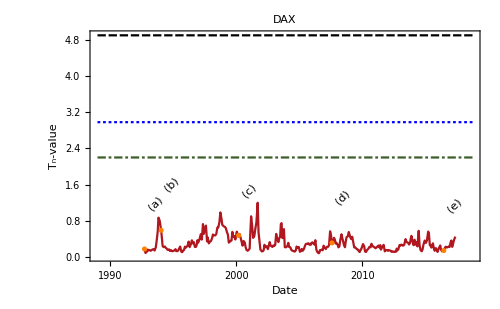
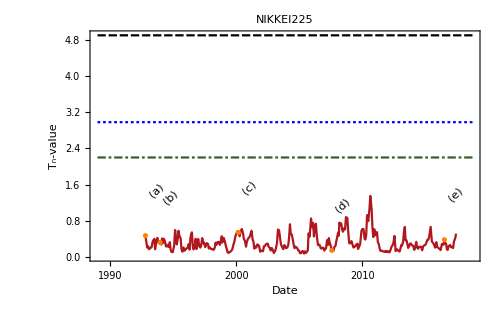

```mathematica
Map[PlotTnCInTimeInCrisis[#,"DatedTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,orderedDatabase]
```

## Simmetry around c = 0

Figure 7

```mathematica
TnZeroInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Block[{parts,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList = Map[{Last[#[[All,1]]],Tn[N[#[[All,2]]],0.0]}&,parts];
Return[CList];
];

newColors = Join[colors,{Orange,Purple,Brown}];
```

```mathematica
PlotTnZeroInTime[market_,returnFunction_,windowSize_:252,skip_:40]:=Block[{plotData,actualReturnType,p,crashLabels,uppList,firstDate,lastDate,legends},
plotData =TnZeroInTime[market,returnFunction,windowSize,skip];
crashLabels = MapThread[
Callout[
ClosestDate[plotData,#1],#2,Above,
LeaderSize->35,CalloutStyle->Directive[Black,Thick],Appearance->"SlantedLabel"
]&,
{market["ImportantDates"],market["ImportantDatesNames"]}
];

firstDate = DateObject[{1989,1,1}];
lastDate = DateObject[{2018,9,24},"Day","Gregorian",-5.];

uppList = Map[{{firstDate, UpperPercentagePoint[#]},{lastDate,UpperPercentagePoint[#]}}&,{0.01,0.05,0.1}];
legends = {Style["T_n(c = 0)",bigFontSize],Style["99% CL",bigFontSize],Style["95% CL",bigFontSize],Style["90% CL",bigFontSize]};

p = DateListPlot[
Append[Join[{plotData},uppList],crashLabels],
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["T_n-value",bigFontSize]},
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotLegends->If[market["Name"]=="DJIA",Placed[LineLegend[legends,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&)],{Right,Top}],None],
PlotMarkers->None,
PlotRange->{{firstDate,lastDate},All},
PlotRangePadding->Automatic,
Joined->{True,True,True,True,False},
PlotStyle->newColors,
PlotLabel->market["Name"]
];
Return[p];
]
```

Simple returns

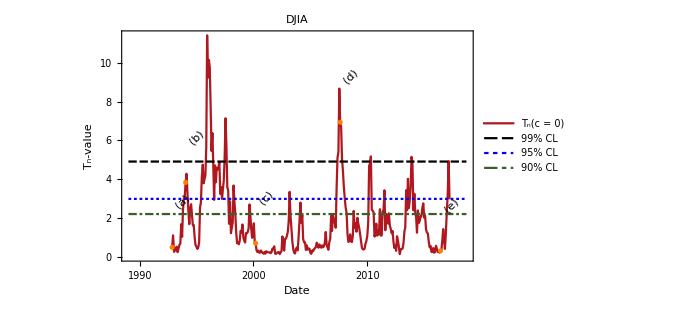
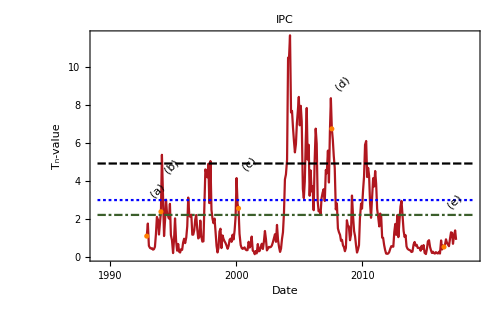
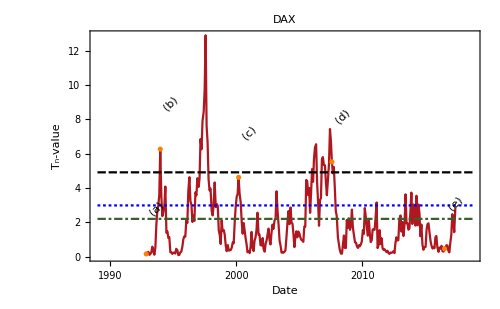
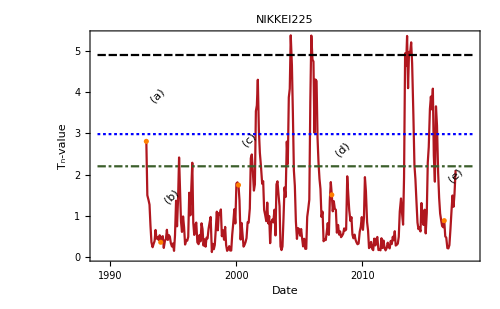

```mathematica
Map[PlotTnZeroInTime[#,"DatedReturns",windowsize,skip]&,orderedDatabase]
```

Trend returns

```mathematica
rules
```

{Japanese asset
price bubble→(a),Tequila effect→(b),Dotcom bubble→(c),Subprime crisis→(d),Brexit→(e)}

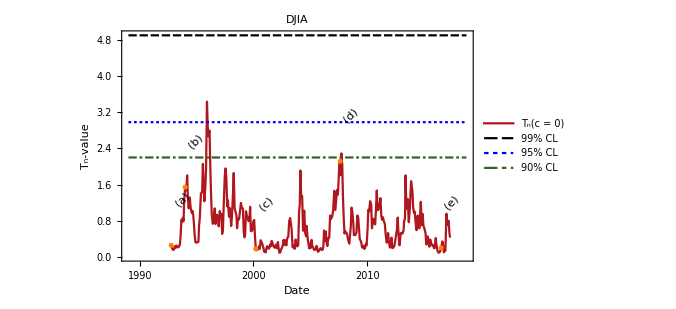
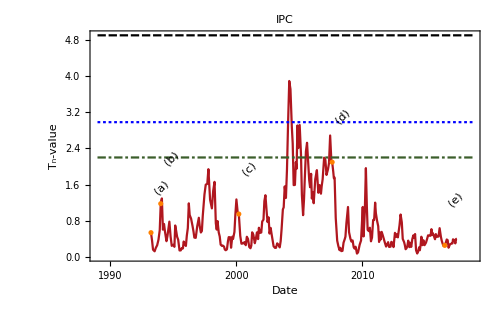
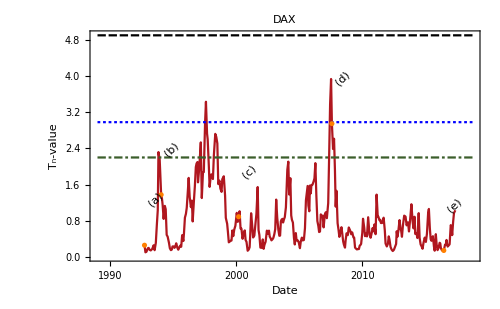
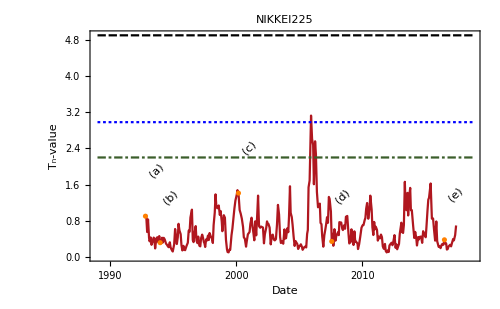

```mathematica
Map[PlotTnZeroInTime[#,"DatedTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,orderedDatabase]
```

Velocities

```mathematica
Map[PlotTnZeroInTimeInCrisis[#,"DatedVelocityTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,orderedDatabase]
```

## Symmetry interval

Figures A.10, A.11 and A.12.

```mathematica
ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];
SymmetryTestInTime[market_,datedreturnType_,CL_,windowsize_,skip_:1]:=Module[{parts,partTr,symTest,plotPoints,means},
parts = Partition[market[datedreturnType], windowsize,skip];
symTest =ProgressParallelMap[
{Middle[#[[All,1]]],MeasureTn[#[[All,2]],CL]}&,
parts,
"Label"->StringJoin["Calculating symmetry interval in time for ",market["Name"]],
Method->"CoarsestGrained"
];
Return[symTest];
];
PlotSymmetryIntervalInTime[market_,returnFunction_,CL_,windowsize_,skip_:1]:=Block[{test,dates,testResults,bestSymmData,crashLabels,legend},
test = SymmetryTestInTime[market,returnFunction,CL,windowsize,skip];
dates = test[[All,1]];
testResults = test[[All,2]];
bestSymmData = Thread[{dates,testResults[[All,"BestSymmetry"]]}];


If[market["Name"] == "DJIA",
legend = Placed[LineLegend[{"C","C_min","C_max"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}];
,
legend = None
];

DateListPlot[
{
Thread[{dates,testResults[[All,"BestSymmetry"]]}],
Thread[{dates,testResults[[All,"PlausibleSymmMin"]]}],
Thread[{dates,testResults[[All,"PlausibleSymmMax"]]}]
}
,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["c",bigFontSize]}, ImageSize->plotSize,
PlotLegends->legend,
BaseStyle->FontSize->smallFontSize,
GridLines->{{},{0}},
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotMarkers->None,
Joined->{True,True,True,False},
PlotStyle->{RGBColor[0., 0.21, 0.52],RGBColor[0., 0.54, 0.51],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[1, 0.5, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2]},
Filling->{2->{3}},
PlotLabel->market["Name"],
PlotRange->All,
PlotRangePadding->Automatic
]
];
```

Simple returns

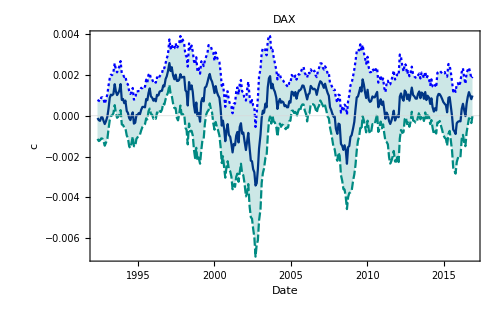
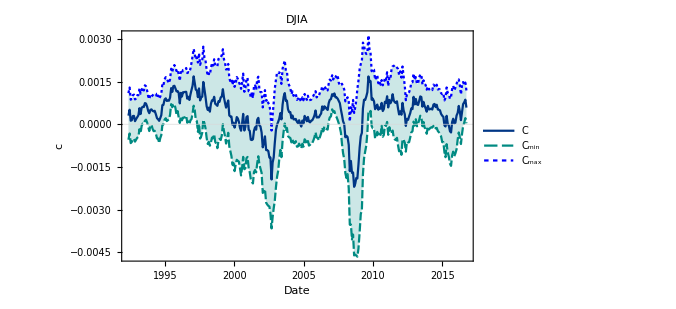
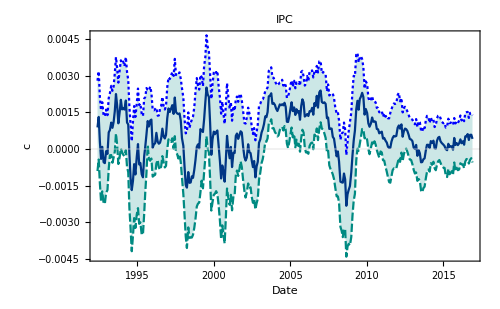
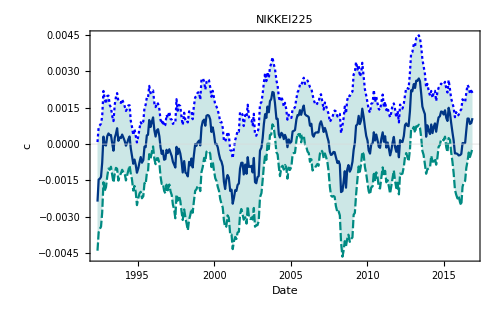

```mathematica
Map[PlotSymmetryIntervalInTime[#,"DatedReturns",0.05,windowsize,skip]&,database]
```

Trend returns

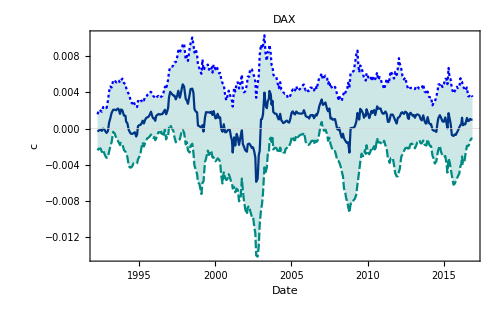
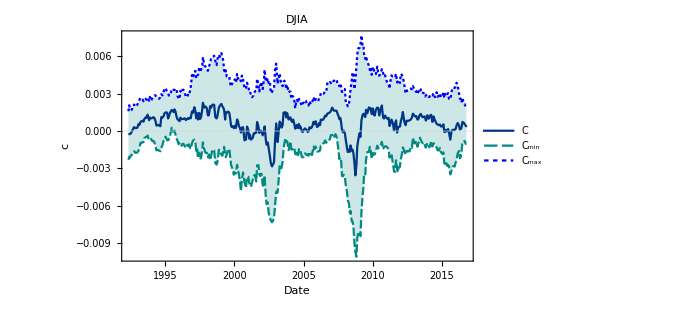
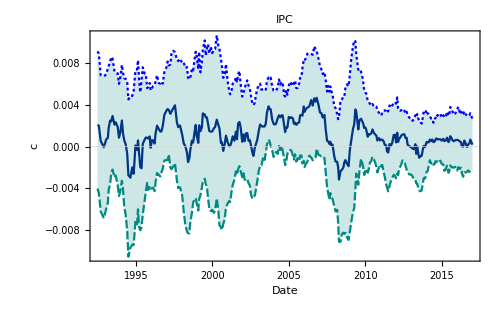
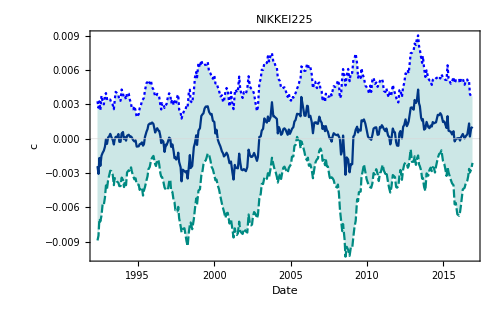

```mathematica
Map[PlotSymmetryIntervalInTime[#,"DatedTrendReturns",0.05,TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

Velocity trend return

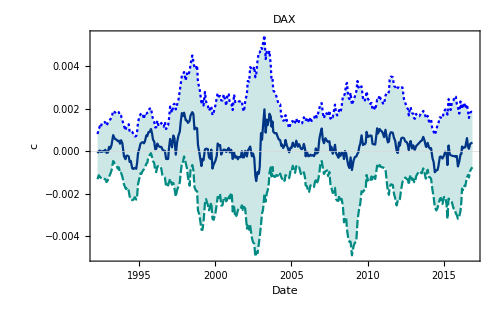
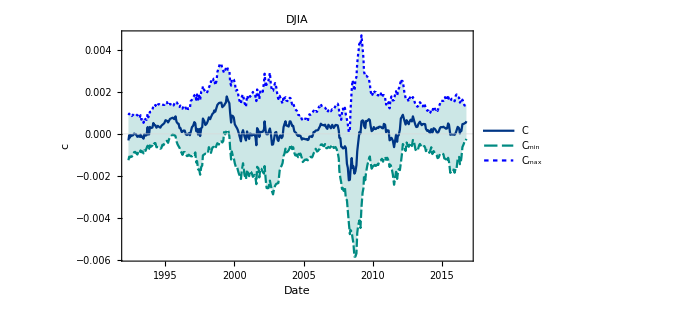
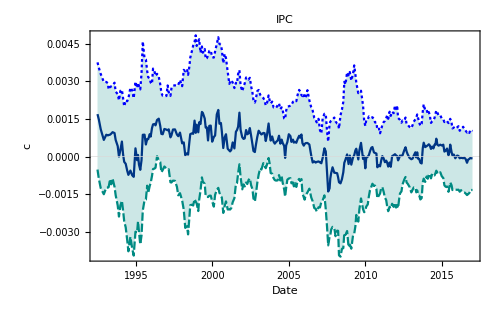
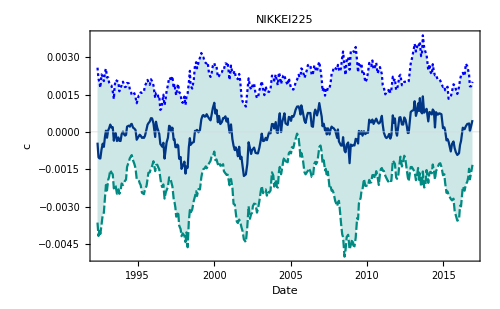

```mathematica
Map[PlotSymmetryIntervalInTime[#,"DatedVelocityTrendReturns",0.05,TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

## Distribution decomposition by runs

Figure 3.

```mathematica
DayLegends[n_Integer]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
Range[n]
];

GroupReturnsByRun[market_,returnType_]:=KeySort[GroupBy[Thread[{TrendDuration[market["Prices"]],market[returnType]}],First->Last]];
PlotTrendDistributionByRuns[market_,returnType_]:=Block[{grouped},
grouped = Select[GroupReturnsByRun[market,returnType],Length[#]>40&];
SmoothHistogram[Take[grouped,4],
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style[returnType/.{"TrendReturns"->"TReturns","VelocityTrendReturns"->"TVReturns"},bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Left,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotLabel->market["Name"]
]
];
```

Trend Returns

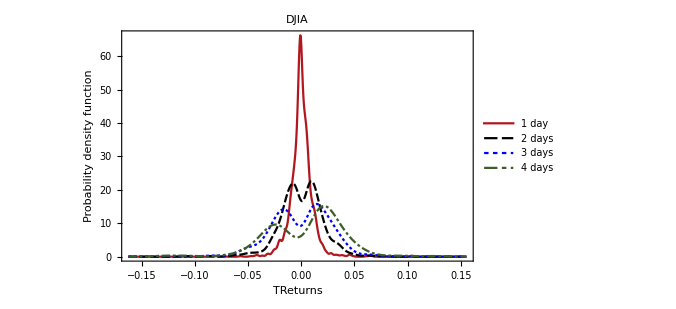
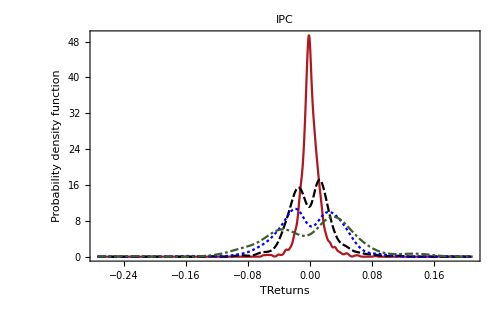
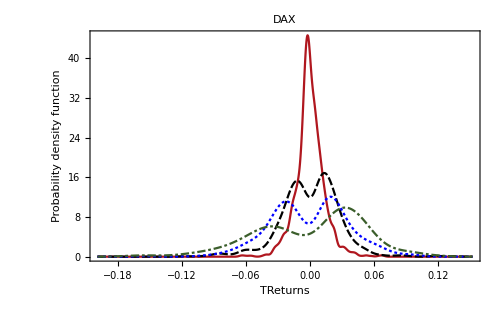
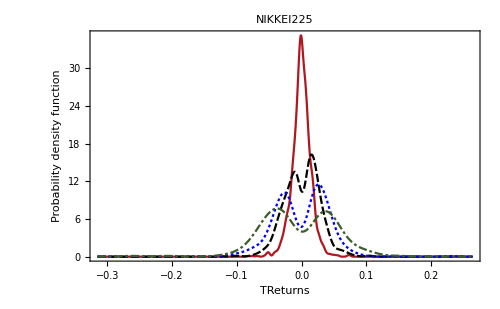

```mathematica
Map[PlotTrendDistributionByRuns[#,"TrendReturns"]&,orderedDatabase]
```

Velocity Trend Returns

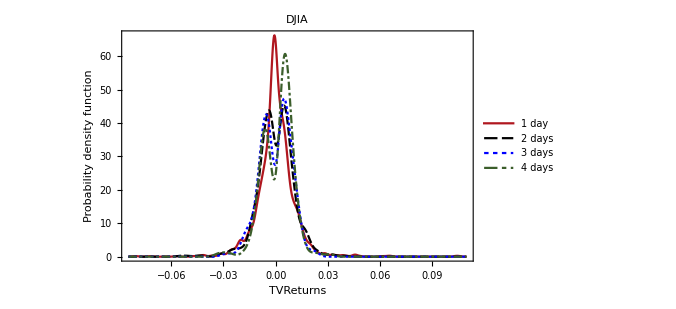
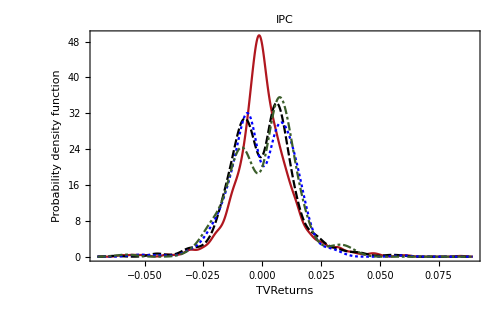
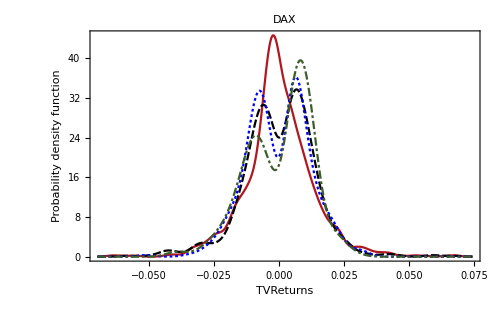
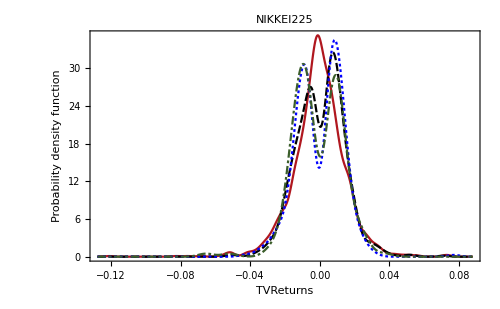

```mathematica
Map[PlotTrendDistributionByRuns[#,"VelocityTrendReturns"]&,orderedDatabase]
```